### Dynamical Systems TIF155/FIM770 Konstantinos Zakkas Problem set 1

### 1.2 Subcritical pitchfork a)

```mathematica
xDot[x_,r_]:=r x+4x^3 - 9x^5
```

```mathematica
sol = Solve[xDot[x,r]==0,x];
X = x/.sol;
roots[r_] = X
```

{0,-1/3 √(2-√(4+9 r)),1/3 √(2-√(4+9 r)),-1/3 √(2+√(4+9 r)),1/3 √(2+√(4+9 r))}

```mathematica
plot1 = Plot[{roots[r][[2]],roots[r][[3]],roots[r][[4]],roots[r][[5]]},{r,-1,1},PlotStyle->{{Red, Dashed},{Red, Dashed},{Red},{Red}}];
plot2 = Plot[roots[r][[1]],{r,-1,0},PlotStyle->{Red}];
plot3 = Plot[roots[r][[1]],{r,0,1},PlotStyle->{Red, Dashed}];

plot = {plot1,plot2,plot3};
Show[plot,AxesLabel->{"r","x"}]
```

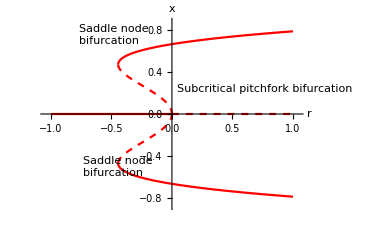

### b)

```mathematica
sols= r/.Solve[xDot[x,r]==0,r];
rF=.;
rF[x_] = sols
```

{-4 x^2+9 x^4}

```mathematica
sol2=Solve[D[rF[x],x]==0]
```

{{x→0},{x→-(√2)/3},{x→(√2)/3}}

```mathematica
rF[x/.sol2[[3]]]
```

{-4/9}